```mathematica
NA = 0.55
α0= ArcSin[NA]
A0=1; (*if well collimated*)
A[α_]:=A0 f Sin[α] Cos[α]^(1/2);
u=k z Sin[α0]^2;
v=k ρ Sin[α0];
In0 := NIntegrate[A[α]Sin[α](1+Cos[α])BesselJ[0,v Sin[α]/Sin[α0]]Exp[I u Cos[α]/Sin[α0]^2],{α,0,α0}];
In1 := NIntegrate[A[α] Sin[α]^2 BesselJ[1,v Sin[α]/Sin[α0]]Exp[I u Cos[α]/Sin[α0]^2],{α,0,α0}];
In2 := NIntegrate[A[α]Sin[α](1-Cos[α])BesselJ[2,v Sin[α]/Sin[α0]]Exp[I u Cos[α]/Sin[α0]^2],{α,0,α0}];
```

# Vector diffraction integrals

### constants and units: set α here with NA of your objective

```mathematica
μB=9.27400915*10^-28;
kb=1.380658*10^-23;
ℏ=6.62606896*10^-34(2π)^-1;
c=299792458;
AMU=1.66*10^-27*kg;
cm=10^-2;mm=10^-3;μm=10^-6;nm = 10^-9;pm=10^-12;fm=10^-15;
kg=1;g=10^-3;ng=10^-9*g;pg=10^-12*g;
Hz=1;kHz=10^3;MHz=10^6;GHz=10^9;
Kk=1;mK=10^-3;μK=10^-6;nK=10^-9;
Ww=1;mW=10^-3;μW=10^-6;nW=10^-9;
Pa=1;GPa=10^9;
ms=10^-3;
ohm=1;V=1;mV=10^-3;
```

```mathematica
nm=10^-9;
μm=10^-6;
```

#### α is NA angle used in calculation below. Enter NA here.

```mathematica
numAP = 0.55
α= ArcSin[numAP]
```

0.55

0.582364

## Vector diff calculation

### Integrals

```mathematica
Clear[r]
```

```mathematica
In0 := NIntegrate[Cos[θ]^(1/2)*Sin[θ](1+Cos[θ])*BesselJ[0,(2π)/(852nm)r*Sin[θ]],{θ,0,α}];
In1 := NIntegrate[Cos[θ]^(1/2)*Sin[θ]^2*BesselJ[1,(2π)/(852nm)r*Sin[θ]],{θ,0,α}];
In2 := NIntegrate[Cos[θ]^(1/2)*Sin[θ](1-Cos[θ])*BesselJ[2,(2π)/(852nm)r*Sin[θ]],{θ,0,α}];
```

```mathematica
α
```

0.582364

### Helicity

```mathematica
gradDataTest = {};
Clear[ϕp]
Do[
r=inc*nm;
ex = -I*(In0+In2*Cos[2ϕp]);
ey=-I*In2*Sin[2ϕp];
ez = -2*In1*Cos[ϕp];
hel =Im[( Cross[{ex,ey,ez}/Norm[{ex,ey,ez}],Conjugate[{ex,ey,ez}]/Norm[{ex,ey,ez}]])]/.ϕp->0;
AppendTo[gradDataTest,{r, hel[[2]]}];
,{inc,1,1500,1}];
```

#### It’s odd so just copying to negative values

```mathematica
gradData = Join[gradDataTest,Map[{-#[[1]],-#[[2]]}&,gradDataTest]];
```

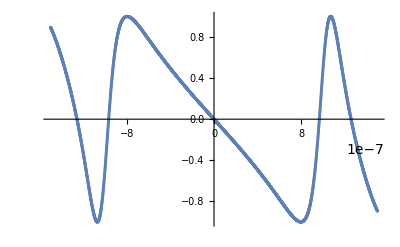

```mathematica
ListPlot[gradData]
```

```mathematica
gradIntUnitless = Interpolation[gradData];
```

```mathematica
gradDataLin = DeleteCases[gradData,x_/;x[[1]]<-.5*10^-7|| x[[1]]>.5*10^-7];
```

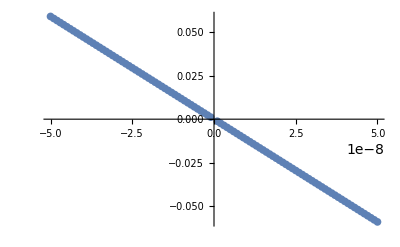

```mathematica
ListPlot[gradDataLin]
```

```mathematica
fitfn = NonlinearModelFit[gradDataLin,a*h,a,h];
```

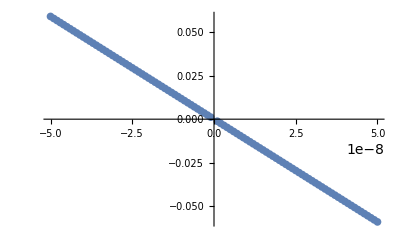

```mathematica
Show[{ListPlot[gradDataLin], Plot[fitfn[h],{h,-.5*10^-7,.5*10^-7}]}]
```

```mathematica
fitfn[h]
```

-1.18048×10^6 h

```mathematica
gradUnitless =( a/.fitfn["BestFitParameters"])*μm
```

-1.18048

#### Using jeff’s formula:

```mathematica
3.1*(0.55)Sin[.55]/(.852)
```

1.04599

```mathematica
(1.18-1.045)/(1.18+1.045)
```

0.0606742

#### Computing vector light shift: no variation along y, only x, and points along y (i.e. look above, we take the second component of hel). Also, taking Im[] gets rid of hte I in Kerman’s expression

```mathematica
λ0:=976nm; λ1=894.59295986 nm; λ2= 852.34727582nm;
```

```mathematica
ω0=2*π*c/λ0;ω1=2*π*c/λ1;ω2=2*π*c/λ2;
```

```mathematica
Δ1=ω0-ω1;Δ2=ω0-ω2;
gf=1/4;-1/4;
mF=4;3;
```

```mathematica
w= 0.71*μm; (*in m*)
```

```mathematica
Clear[U0]
```

```mathematica
mK=10^-3;
```

```mathematica
U0[x_]= 1.2mK*Exp[-2*x^2/(w^2)];
```

```mathematica
U0[1μm]
```

0.0000227056

```mathematica
Beffy[x_ ] =U0[x]*kb 1/2*(Δ2-Δ1)/(Δ2/2+Δ1)gradIntUnitless[x]*1/μB*gf*mF;
```

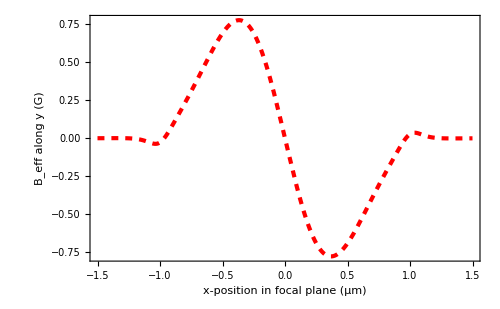

```mathematica
Plot[Beffy[x*μm ],{x,-1.5,1.5}, Frame-> True,FrameLabel-> {"x-position in focal plane (μm)","B_eff along y (G)"}, PlotStyle->{Red,Dashed,Thickness-> .006},LabelStyle-> {Black, FontSize-> 22}, ImageSize-> 500, FrameStyle-> Thickness[.004]]
```

```mathematica
2.6/3.1
```

0.83871

```mathematica
gradDataLinB =Table[{x,Beffy[x ]},{x,-100nm,100nm,1nm}];
```

```mathematica
fitfn = NonlinearModelFit[gradDataLinB ,a*h,a,h]
```

FittedModel[-3.40814×10^6 h]

```mathematica
Print["Gradient is " <>ToString[(a/.fitfn["BestFitParameters"])μm]<>" G/"<>"μm" ]
```

Gradient is -3.40814 G/μm

```mathematica
Print["Total Variation over plus/minus 50nm is " <>ToString[(a/.fitfn["BestFitParameters"])100nm]<>" G" ]
```

Total Variation over plus/minus 50nm is -0.340814 G

### Comparing gradient to Jeff: agrees to 10%

```mathematica
(3.1*(0.55)Sin[.55]/(.976)(Δ2-Δ1)/(Δ2+2Δ1)*gf*mF)1.2mK*kb/μB
```

2.26191